```mathematica
(*
e[x]_here = e_1(x)_{Lagrangian approach};
v[x]_here = {v^1(x)}_{Lagrangian approach};
σ[x]_here  = σ(x)_{Lagrangian approach};
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ψ[x]∈Reals};
```

```mathematica
e[x_]:={Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ψ'[x]}}

```mathematica
b[x_]:={{-ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-1/2 ψ'[x]

```mathematica
H[x_]:=-1/2 ψ'[x]
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:={{{0}}}
```

```mathematica
eqσ=FullSimplify[v'[x]-2 H[x]w[x]==0,Assumptions->ass]
```

```mathematica
eqv=FullSimplify[ρ(v[x]v'[x]-2 v[x]w[x]gc[x][[1,1]]b[x][[1,1]]-w[x]gc[x][[1,1]]w'[x])
-gc[x][[1,1]]σ'[x]
-2 η(v''[x] - (w'[x]b[x][[1,1]]+w[x] b'[x][[1,1]])),Assumptions->ass]
```

```mathematica
eqψ=FullSimplify[{ρ v[x](v[x]b[x][[1,1]]+w'[x])
-κ( - 2 H''[x]-4H[x](H[x]^2-K[x]))
-2 σ[x]H[x]
- 2η( v'[x]b[x][[1,1]]-2 w[x]*(2 H[x]^2-K[x]))==0},Assumptions->ass]
eqw={w[x]==0}
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
ρ=1;
η=1;
σc=1;
xmin=1;
xmax=3;
vmin=1;
wmin=0;
wmax=0;
sigmamax=1;
ψmin=1;
ψmax=2.5;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check v*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/v.csv"];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,1.},{2.9,1.},{2.8,1.},{2.7,1.},{2.6,1.},{2.5,1.},{2.4,1.},{2.3,1.},{2.2,1.},{2.1,1.},{2.,1.},{1.9,1.},{1.8,1.},{1.7,1.},{1.6,1.},{1.5,1.},{1.4,1.},{1.3,1.},{1.2,1.},{1.1,1.},{1.,1.}}

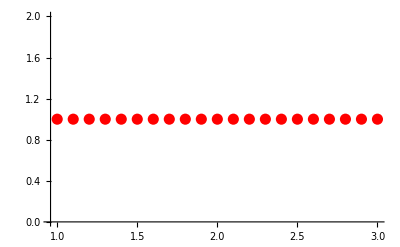

```mathematica
plotvnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
(*check w*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/w.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,0.},{2.9,0.},{2.8,0.},{2.7,0.},{2.6,0.},{2.5,0.},{2.4,0.},{2.3,0.},{2.2,0.},{2.1,0.},{2.,0.},{1.9,0.},{1.8,0.},{1.7,0.},{1.6,0.},{1.5,0.},{1.4,0.},{1.3,0.},{1.2,0.},{1.1,0.},{1.,0.}}

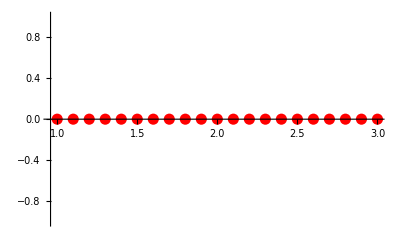

```mathematica
plotwnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
(*check sigma*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/sigma.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,1.},{2.9,1.},{2.8,1.},{2.7,1.},{2.6,1.},{2.5,1.},{2.4,1.},{2.3,1.},{2.2,1.},{2.1,1.},{2.,1.},{1.9,1.},{1.8,1.},{1.7,1.},{1.6,1.},{1.5,1.},{1.4,1.},{1.3,1.},{1.2,1.},{1.1,1.},{1.,1.}}

```mathematica
plotσnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

-Graphics-

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,2.44006},{2.8,2.34011},{2.7,2.20067},{2.6,2.02314},{2.5,1.81039},{2.4,1.56725},{2.3,1.30092},{2.2,1.02078},{2.1,0.737731},{2.,0.462992},{1.9,0.206844},{1.8,-0.0223454},{1.7,-0.218542},{1.6,-0.377921},{1.5,-0.498397},{1.4,-0.57904},{1.3,-0.619549},{1.2,-0.61987},{1.1,-0.580003},{1.,-0.5}}

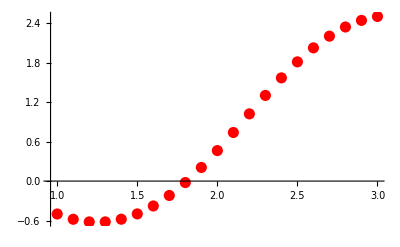

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
Show[plotψnum]
```

-Graphics-

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{0.781036,-0.491621},{0.859564,-0.429718},{0.932894,-0.361742},{0.997573,-0.285492},{1.04939,-0.199986},{1.08361,-0.106055},{1.09566,-0.00683002},{1.08226,0.0922048},{1.04256,0.183901},{0.978883,0.260888},{0.89643,0.317298},{0.802038,0.350034},{0.702528,0.359074},{0.603341,0.346865},{0.507864,0.31728},{0.417434,0.27465},{0.331731,0.223147},{0.249296,0.166543},{0.168031,0.108267},{0.0856334,0.0516112},{0.,0.}}

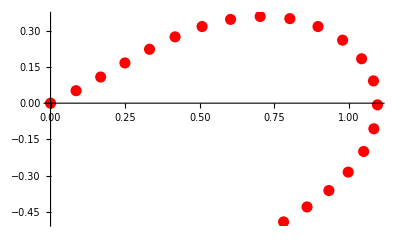

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

```mathematica
Show[plotXnum]
```

-Graphics-